# Projections

```mathematica
ψ = Sum[c[G]*Exp[ⅈGr],G]/Sqrt[vol];
```

```mathematica
Clear[L,k];
g1[x_,y_]:=Sin[κ*x]*Sin[κ*y];
g2[x_,y_]:=Sin[κ*x]*Cos[κ*y];
g3[x_,y_]:=Cos[κ*x]*Sin[κ*y];
basVec[x_,y_]:= Exp[-ⅈ*(Gx*x+Gy*y)]/Sqrt[vol];

κ=π/2;
ContourPlot[g1[x,y]^2,{x,0,2},{y,0,2},PlotLegends->Automatic]
ContourPlot[g2[x,y]^2,{x,0,2},{y,0,2},PlotLegends->Automatic]
ContourPlot[g3[x,y]^2,{x,0,2},{y,0,2},PlotLegends->Automatic]
Clear[κ];
tmp = Integrate[basVec[x,y]*g2[x,y],{x,xL,xR},{y,yL,yR}];
Simplify[Numerator[tmp]]
Simplify[Denominator[tmp]]
```

## 3 Trial Orbitals per well

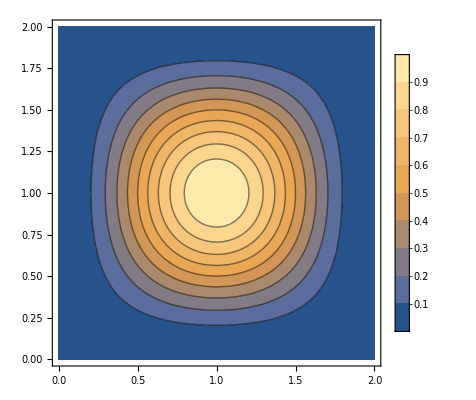

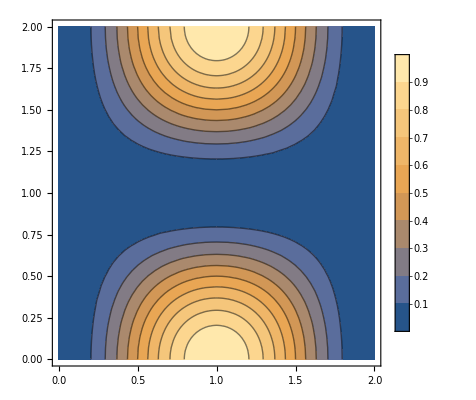

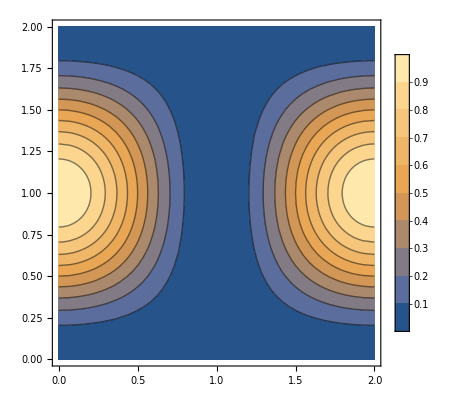

(-ⅇ^(-ⅈ Gx xL) (κ Cos[xL κ]+ⅈ Gx Sin[xL κ])+ⅇ^(-ⅈ Gx xR) (κ Cos[xR κ]+ⅈ Gx Sin[xR κ])) (ⅇ^(ⅈ Gy yR) (-ⅈ Gy Cos[yL κ]+κ Sin[yL κ])+ⅈ ⅇ^(ⅈ Gy yL) (Gy Cos[yR κ]+ⅈ κ Sin[yR κ]))

ⅇ^(ⅈ Gy (yL+yR)) √vol (Gy-κ) (Gy+κ) (Gx^2-κ^2)